```mathematica
ℏc=197.3;T0=1;μB0=1;μS0=1;μQ0=1;c=4;
P[T_,μB_,μS_,μQ_]:=c(T0/ℏc)^4((T/T0)^2+(μB/μB0)^2+(μS/μS0)^2+(μQ/μQ0)^2)^2;
s[T_,μB_,μS_,μQ_]:=ℏc D[P[T,μB,μS,μQ],T]//Evaluate;
ρB[T_,μB_,μS_,μQ_]:=ℏc D[P[T,μB,μS,μQ],μB]//Evaluate;
ρS[T_,μB_,μS_,μQ_]:=ℏc D[P[T,μB,μS,μQ],μS]//Evaluate;
ρQ[T_,μB_,μS_,μQ_]:=ℏc D[P[T,μB,μS,μQ],μQ]//Evaluate;
ϵ[T_,μB_,μS_,μQ_]:=-P[T,μB,μS,μQ]+(T s[T,μB,μS,μQ]+μB ρB[T,μB,μS,μQ]+μQ ρQ[T,μB,μS,μQ]+μS ρS[T,μB,μS,μQ])/ℏc//Evaluate;
(*ϵ[T,μB,μS,μQ]==3P[T,μB,μS,μQ]//FullSimplify*)
```

```mathematica
ϵ[159.285,17.542,17.542,17.542]
ρB[159.285,17.542,17.542,17.542]
ρS[159.285,17.542,17.542,17.542]
ρQ[159.285,17.542,17.542,17.542]
```

5.47539

0.960924

0.960924

0.960924

```mathematica
Plot3D[(2x y)/(1+x^2+y^2),{x,0,10},{y,0,10}]
```

-Graphics3D-

```mathematica
Flatten[Table[{r Cos[ϕ],r Sin[ϕ]},{r,1/10,10,1/10},{ϕ,0,2π,(2π)/1000}],1]//Length
```

100100

```mathematica
e0=1;q=1;ρB0=1/2;ρS0=1/2;ρQ0=1/2;
eGubser[τ_,r_]:=e0/τ^4(2q τ)^(8/3)/((1+2 q^2(τ^2+r^2)+q^4(τ^2-r^2)^2)^(4/3));
ρBGubser[τ_,r_]:=ρB0/τ^3(4 q^2 τ^2)/((1+2 q^2(τ^2+r^2)+q^4(τ^2-r^2)^2)^2);
ρSGubser[τ_,r_]:=ρS0/τ^3(4 q^2 τ^2)/((1+2 q^2(τ^2+r^2)+q^4(τ^2-r^2)^2)^2);
ρQGubser[τ_,r_]:=ρQ0/τ^3(4 q^2 τ^2)/((1+2 q^2(τ^2+r^2)+q^4(τ^2-r^2)^2)^2);
eGubser[0.6,0.1]
ρBGubser[0.6,0.1]
ρSGubser[0.6,0.1]
ρQGubser[0.6,0.1]
```

5.47541

0.960918

0.960918

0.960918

```mathematica
Flatten[Table[{r Cos[ϕ],r Sin[ϕ]},{r,0,5,1/100},{ϕ,0,2π,(2π)/1000}],1]//Length
```

501501

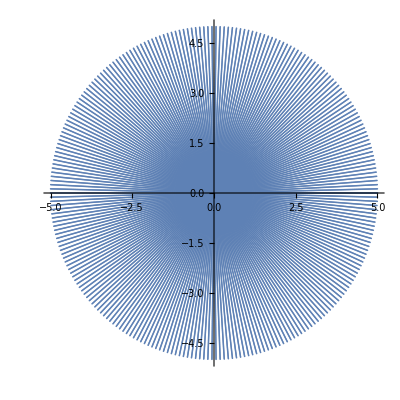

```mathematica
ListPlot[Flatten[Table[{r Cos[ϕ],r Sin[ϕ]},{r,0,5,2/100},{ϕ,0,2π,(2π)/250}],1],AspectRatio->1]
```